```mathematica
ClearAll[kx];
n=50;
mu=0.1;
o={{0,0},{0,0}};
bands={};
probability1={};
probability2={};

For[kx=-Pi,kx≤Pi,kx+=Pi/100.,

diag={{1+2*mu*Cos[kx],-2*mu*Sin[kx]},{-2*mu*Sin[kx],-(1+2*mu*Cos[kx])}};
offdiag={{mu,-mu},{mu,-mu}};

tab=Table[
diag*KroneckerDelta[i,j]
+offdiag*KroneckerDelta[j,i+1]
+ConjugateTranspose[offdiag]*KroneckerDelta[j,i-1]
,{i,1,n},{j,1,n}];
H=ArrayFlatten[tab];
energy=Eigenvalues[H];
{psi1,psi2}=Eigenvectors[H,-2];
Pedge1=psi1[[1]]^2+psi1[[2]]^2+psi1[[2n-1]]^2+psi1[[2n]]^2;
AppendTo[probability1,{kx,Pedge1}];
Pedge2=psi2[[1]]^2+psi2[[2]]^2+psi2[[2n-1]]^2+psi2[[2n]]^2;
AppendTo[probability2,{kx,Pedge2}];

For[i=0,i≤2n,i++,
AppendTo[bands,{kx,energy[[i]]}];
]
]
```

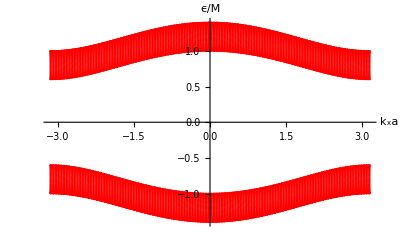

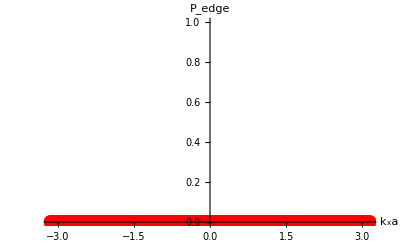

```mathematica
ListPlot[bands,AxesLabel->{"k_xa","ϵ/M"},PlotStyle->{Red,PointSize[.003]},AxesStyle->Directive[Black, 12]]
ListPlot[probability1,AxesLabel->{"k_xa","P_edge"},PlotStyle->{Red,PointSize[.025]},AxesStyle->Directive[Black, 12],PlotRange->{0,1}]
```